```mathematica
gauss[x_,u_]:=(Exp[-(x/u)^2/2]/Sqrt[Sqrt[Pi]u]);
(*nie gauss zwykly ma sie calkowac do 1 tylko |gauss|^2*)
ψ[x_]:=gauss[x,l];
Print["<ψ|ψ> =?= 1"]
Assuming[{l>0},Integrate[ψ[x]^2,{x,-Infinity,Infinity}]]
```

<ψ|ψ> =?= 1

1

```mathematica
kin=Assuming[{l>0,hbar>0},Integrate[
Conjugate[ψ[x]](-hbar^2D[ ψ[x],x,x]/2/m)
,{x,-Infinity,Infinity}]]

int=Assuming[{l>0},Integrate[
Conjugate[ψ[x]]Conjugate[ψ[y]]DiracDelta[x-y]ψ[y]ψ[x]
,{x,-Infinity,Infinity},{y,-Infinity,Infinity}]]

energy=n kin+n(n-1)/2 g int
```

hbar^2/(4 l^2 m)

1/(l √(2 π))

(hbar^2 n)/(4 l^2 m)+(g (-1+n) n)/(2 l √(2 π))

ekstremum:

{l→-(hbar^2 √(2 π))/(g m (-1+n))}

2.50663

energia w ekstremum:

-(g^2 m (-1+n)^2 n)/(8 hbar^2 π)

-0.0795775

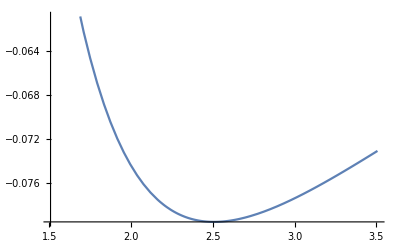

```mathematica
pod={m->1,hbar->1,g->-1,n->2};
Print["ekstremum:"]
sol=Solve[D[energy,l]==0,{l}][[1]]
nlextr=N[l/.sol/.pod]
Print["energia w ekstremum:"]
eextr=Simplify[energy/.sol]
neextr=N[eextr/.pod]
Plot[energy/.pod/.{l->xx},{xx,nlextr-1,nlextr+1}]
```